```mathematica
results = Table[Sum[Sum[Abs[Log[j/i]*j ] , {i, j, N}], {j, 1, N}], {N, 100, 110}]//N
```

{84532.3,87081.9,89682.3,92333.9,95037.3,97792.9,100601.,103463.,106378.,109348.,112372.}

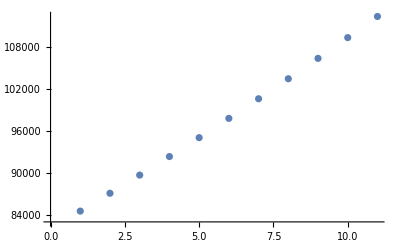

```mathematica
ListPlot[results]
```

```mathematica
Series[(Sin[ω * ti] * Sin[ω * tj]) - (Sin[ω * (ti+δ)] * Sin[ω * tj]) - (Sin[ω * (tj+δ)] * Sin[ω * ti]) +  (Sin[ω * (ti + δ)] * Sin[ω * (tj + δ)]), {δ, 0 , 4}]
```

ω^2 Cos[ti ω] Cos[tj ω] δ^2+1/2 (-ω^3 Cos[tj ω] Sin[ti ω]-ω^3 Cos[ti ω] Sin[tj ω]) δ^3+1/12 (-4 ω^4 Cos[ti ω] Cos[tj ω]+3 ω^4 Sin[ti ω] Sin[tj ω]) δ^4+O[δ]^5

```mathematica
Sum[Sum[i*j, {i, 0, N}], {j, 0, N}]
```

1/4 N^2 (1+N)^2

```mathematica
FourierTransform[Sin[Sin[a*t]], t,ω]
```

$Aborted

```mathematica
Series[(Sin[t+δ]-Sin[t])/ω, {δ,0, 2}]
```

(Cos[t] δ)/ω-(Sin[t] δ^2)/(2 ω)+O[δ]^3

```mathematica
Cos[x]^5*Sin[x]^2//TrigExpand
```

Cos[x]^5 Sin[x]^2